# ランチェスターの法則（1次法則）

## プログラム前の注意点

```mathematica
以下ではローカルに変数を代入するためにModule[]を使う
```

```mathematica
a=.;b=.
```

```mathematica
Module[{a=3,b=5},a+b]
a+b
```

## プログラミングでよく使う内蔵関数

#### If文について

```mathematica
If[condition,t,f]
condition の評価の結果がTrueとなる場合に t を，Falseとなる場合に f を返す．
```

```mathematica
a=3;
If[a>1,1000,-1000]
```

```mathematica
If[a>5,1000,-1000]
```

```mathematica
If[]をTableに入れることもできる．
```

```mathematica
x={1,2,3,4,5,6};
Table[If[x⟦i⟧>3,1000,-1000],{i,1,5}]
```

```mathematica
問題：おみくじを作ってみよう
1.乱数を発生させる
2.乱数が0～0.2の間の数なら大吉，
0.2～0.4の間なら中吉，
などのルールをIf文で書く
3.　関数omikujiを定義する
4.　今日の運勢は？
```

#### Appendの使い方

```mathematica
Append[{a,b,c,d},x]
```

```mathematica
x={};
Append[x,1]
```

```mathematica
(* Appendを反復的に繰り返す *)
x={};
Do[x=Append[x,i],{i,1,10}];
x
```

#### RandomSampleの使い方

```mathematica
RandomSample[{1,2,3,4,5}]
```

#### Do 繰り返し (Forを簡略化したもの)

```mathematica
{{, Do[expr,{Subscript[i, max]}]
式expr をSubscript[i, max] 回評価する．}}
{{, Do[expr,{i,Subscript[i, max]}]
変数 i の値が1から Subscript[i, max] まで刻み幅1で式 expr を順に評価する．}}
```

```mathematica
(*　最初にx=5を代入して，次にxにx+1を再帰的に代入する．これを10回繰り返す　*)
x=5;
Do[x=x+1,{10}];
x
```

15

```mathematica
(* Doそのものはvoid関数である．よってデフォルトの出力はない *)
x=5;
Do[x=x+1,{10}]
```

#### While（条件を満たす限り繰り返す）

```mathematica
n<4という条件を満足させながら，n を出力し1つずつ増加させる
```

```mathematica
n=1;While[n<4,Print[n];n++]
```

1

2

3

## ワンショット

```mathematica
次のような状況をプログラムで表現してみよう．

グループ1とグループ2の戦士が招集される．
初期条件として各兵士の武力は正規分布にしたがう．
兵士達は敵国の兵士と，騎士道精神に則り一対一で戦う．(対戦はランダム)
なおx,yを兵数として，戦闘能力をそれぞれa,bとおけば，微分方程式は
dx/dt==-b,dy/dt==-a
である
```

### 1回の戦闘結果を出力するModule

```mathematica
(* ここで各国の兵数を一般化する *)
Module[{id1,id2,n1=20,n2=20,power1,power2,winner1,winner2},
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

(*兵力*)
power1=Table[RandomReal[NormalDistribution[50,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[51,1]],{n2}];

(* 戦闘力を比較して勝者を残す*)
winner1={};
winner2={};

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[n1,n2]}](* Table *);

Print[{グループ1戦闘後,winner1}];
Print[{グループ2戦闘後,winner2}];
Print[{"戦闘力の組み合わせ",MatrixForm[Table[{i,N[power1⟦i⟧,3],N[power2⟦i⟧,3]},{i,1,Min[n1,n2]}]]}]
]
```

{ー グル プ1戦闘後,{}}

{ー グル プ2戦闘後,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}}

{戦闘力の組み合わせ,(1 | 49.5321 | 50.229
2 | 49.9137 | 51.2748
3 | 51.1351 | 53.7604
4 | 49.1489 | 50.872
5 | 50.4876 | 51.3145
6 | 50.2007 | 52.7917
7 | 48.9579 | 50.4654
8 | 49.3318 | 50.6185
9 | 49.2707 | 51.3208
10 | 49.9689 | 51.2805
11 | 49.9008 | 51.0453
12 | 48.0213 | 51.1775
13 | 50.5272 | 50.6905
14 | 47.9872 | 50.3475
15 | 49.9049 | 51.8186
16 | 51.1981 | 51.3673
17 | 49.9932 | 51.6758
18 | 50.6235 | 52.1548
19 | 49.6602 | 50.8396
20 | 50.475 | 51.9917)}

### For文 を使った別の表現

```mathematica
Module[{army1,army2,winner1={},winner2={},list1={}},
For[i=1,i<=20,i++,
army1=RandomReal[NormalDistribution[50,1]];
army2=RandomReal[NormalDistribution[52,2]];
list1=Append[list1,{i,army1,army2}];
If[army1>army2,winner1=Append[winner1,army1],
winner2=Append[winner2,army2]]
](* For終了 *);
Print[{"army1戦闘後 ",winner1}];
Print[{"army2戦闘後 ",winner2}];
Print[{"戦闘力の組み合わせ",MatrixForm[list1]}]
]
```

{army1戦闘後 ,{51.8453}}

{army2戦闘後 ,{54.3301,51.8736,52.2632,51.9913,51.5798,53.5911,48.9883,50.9706,53.7025,51.1508,51.8495,50.9053,54.0601,50.9572,55.6151,51.5122,52.1038,54.5547,50.7057}}

{戦闘力の組み合わせ,(1 | 50.7 | 54.3301
2 | 49.2653 | 51.8736
3 | 49.7083 | 52.2632
4 | 49.4863 | 51.9913
5 | 50.2898 | 51.5798
6 | 48.685 | 53.5911
7 | 47.8909 | 48.9883
8 | 49.883 | 50.9706
9 | 51.8453 | 47.6762
10 | 51.6976 | 53.7025
11 | 50.0095 | 51.1508
12 | 50.8303 | 51.8495
13 | 48.6184 | 50.9053
14 | 50.4019 | 54.0601
15 | 50.1492 | 50.9572
16 | 50.2509 | 55.6151
17 | 49.1955 | 51.5122
18 | 50.3148 | 52.1038
19 | 49.9562 | 54.5547
20 | 50.0755 | 50.7057)}

```mathematica
問題
より興味深いシミュレーションにするためには,どのようなシナリオを追加すればよいか?
```

## 反復プログラミングの手順

### 国1と国2の戦士が同数招集される．初期条件として各兵士の武力は正規分布にしたがう．

```mathematica
Module[{id1,id2,power1,power2,n=10},
id1=Range[n];id2=Range[n];(*　兵士の番号を出力　*)
power1=Table[RandomReal[NormalDistribution[10,1]],{n}];(*　1国兵士の武力を定義する　*)
power2=Table[RandomReal[NormalDistribution[12,1]],{n}];(*　2国兵士の武力を定義する　*)
Print[{power1,power2}];
id1=RandomSample[id1];
id2=RandomSample[id2];(*　ランダムに並び替える　*)
Print[{id1,id2}];
power1=Table[power1⟦id1⟦i⟧⟧,{i,1,n}];
power2=Table[power2⟦id1⟦i⟧⟧,{i,1,n}];
Print[{power1,power2}](* id1,id2の番号で呼び出した兵士の兵力 *)
]
```

{{10.3669,10.7537,10.9809,11.1658,9.67576,9.28828,9.21689,9.9837,8.99814,8.94759},{12.222,11.3155,11.1179,13.2001,11.942,13.4868,12.2957,12.5764,10.3736,12.0089}}

{{9,10,4,5,7,3,8,6,1,2},{3,5,1,6,2,9,7,8,4,10}}

{{8.99814,8.94759,11.1658,9.67576,9.21689,10.9809,9.9837,9.28828,10.3669,10.7537},{10.3736,12.0089,13.2001,11.942,12.2957,11.1179,12.5764,13.4868,12.222,11.3155}}

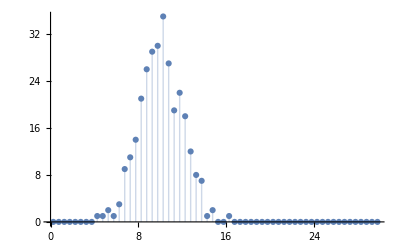

```mathematica
(* 兵力分布をグラフで確認してみる　*)
Module[{dist,bin,memori},
dist=Table[RandomReal[NormalDistribution[10,2]],{300}];
bin=BinCounts[dist,{0,30,0.5}];
(* 0.5の幅に何人いるかをカウント．distをそのままプロットしても意味無し *)
memori=Table[i,{i,0.25,30,0.5}];(* 目盛りを定義 *)
ListPlot[Transpose[{memori,bin}],Filling->Axis]
]
```

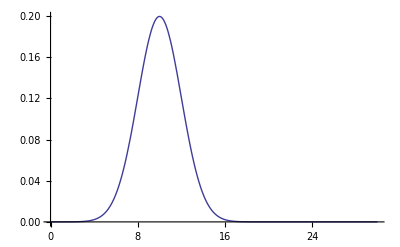

```mathematica
(* 理論値の分布 *)
Plot[PDF[NormalDistribution[10,2],x],{x,0,30}]
```

### 兵士達はランダムマッチングにより一対一で戦う．

```mathematica
(* ここで各国の兵数を一般化する *)
Module[{id1,id2,n1=15,n2=15,power1,power2,winner1,winner2},
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

id1=RandomSample[Range[n1]];
id2=RandomSample[Range[n2]];(*　ランダムに並び替える　*)
{id1,id2}
]
```

{{7,24,27,22,30,11,16,14,21,23,18,9,4,25,12,26,6,8,1,10,28,5,3,2,20,19,17,29,13,15},{21,18,22,9,26,19,30,11,29,1,16,4,17,15,27,23,13,25,14,6,24,5,3,2,12,8,28,10,7,20}}

```mathematica
Q ランダムマッチングで順序対を作りなさい
```

### 対戦した兵士のうち，武力の高い兵士が勝負に勝ち，次の対戦に進む．

```mathematica
(* ここで各国の兵数を一般化する *)
Module[{id1,id2,n1=30,n2=30,power1,power2,winner1,winner2},
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

id1=RandomSample[Range[n1]];
id2=RandomSample[Range[n2]];(*　ランダムに並び替える　*)
winner1=Table[
If[power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,id1⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
winner1=Select[winner1,#>0&];Print[{"戦闘後1",winner1}];

winner2=Table[
If[power1⟦id1⟦i⟧⟧<power2⟦id2⟦i⟧⟧,id2⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
winner2=Select[winner2,#>0&];Print[{"戦闘後2",winner2}];
]
```

{戦闘後1,{20,5,23,9,18,21}}

{戦闘後2,{14,12,21,1,6,4,19,10,17,29,8,11,22,18,3,23,26,27,30,13,7,28,20,15}}

## 反復

### 片方の集団が全滅するまで戦闘を反復するModule

```mathematica
Module[{id1,id2,n1=10,n2=10,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
8.89909 | 10.8493 | 8.60179 | 10.0509 | 10.619 | 10.434 | 10.3921 | 9.71153 | 10.2917 | 11.4429

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
10.1767 | 9.05101 | 10.8939 | 10.3497 | 10.7659 | 10.1089 | 9.66295 | 11.9711 | 10.7933 | 11.5292

{G1:出撃する兵士のID,{1,6,2,7,4,3,5,8,10,9}}

{G2:出撃する兵士のID,{1,9,5,8,7,2,3,4,10,6}}

{G1:戦闘で勝った兵士,{2,4,9}}

{G2:戦闘で勝った兵士,{1,9,8,2,3,4,10}}

{G1:残存兵,{2,4,9}}

{G2:残存兵,{1,9,8,2,3,4,10}}

{G1:出撃する兵士のID,{2,9,4}}

{G2:出撃する兵士のID,{1,8,4,10,3,9,2}}

{G1:戦闘で勝った兵士,{2}}

{G2:戦闘で勝った兵士,{8,4}}

{G1:残存兵,{2}}

{G2:残存兵,{8,4,10,3,9,2}}

{G1:出撃する兵士のID,{2}}

{G2:出撃する兵士のID,{3,4,8,2,9,10}}

{G1:戦闘で勝った兵士,{}}

{G2:戦闘で勝った兵士,{3}}

{G1:残存兵,{}}

{G2:残存兵,{3,4,8,2,9,10}}

### Q 上記アルゴリズムが正しければ，武力の高い兵士（呂布）はたった一人でも生き残るはずである

```mathematica
呂布が生き残るかどうか確認せよ
```

```mathematica
power1=Append[power1,100]//Flatten;(* 戦闘力100（呂布）を追加するコマンド例 *)
```

### 解答例

```mathematica
(*片方の集団が全滅するまで戦闘を反復するModule *)
Module[{id1,id2,n1=50,n2=50,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1-1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)
power1=Append[power1,100]//Flatten;(* 戦闘力100（呂布）を追加するコマンド例 *)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
](* while *)
]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
11.1179 | 12.734 | 8.72881 | 9.26854 | 11.3763 | 10.9291 | 11.2349 | 9.24062 | 10.989 | 8.21829 | 8.44063 | 9.12502 | 9.75568 | 10.8067 | 10.7372 | 10.7373 | 9.42388 | 9.83136 | 11.1806 | 12.5942 | 7.94793 | 10.2956 | 10.426 | 11.9969 | 11.3772 | 9.79795 | 10.8416 | 10.5985 | 9.5341 | 10.2562 | 12.0863 | 9.71974 | 10.5225 | 9.22418 | 9.15052 | 10.0428 | 9.28296 | 9.60802 | 9.39332 | 9.12018 | 10.2576 | 10.8827 | 11.8793 | 10.4159 | 10.1112 | 10.4714 | 10.4555 | 10.7371 | 10.6575 | 100

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
9.28829 | 10.0054 | 9.92914 | 11.0103 | 10.7581 | 9.3866 | 10.6902 | 10.4609 | 8.64471 | 11.5288 | 9.02706 | 12.7507 | 11.4866 | 10.1172 | 8.74266 | 10.251 | 10.2482 | 11.449 | 10.7845 | 11.9083 | 10.7563 | 12.324 | 11.3869 | 11.3651 | 11.6533 | 8.58753 | 9.0737 | 10.9967 | 11.1743 | 11.32 | 12.175 | 11.3148 | 10.8731 | 10.867 | 9.68168 | 9.92568 | 10.0383 | 11.1699 | 9.55297 | 9.7036 | 11.3574 | 11.0027 | 12.0652 | 10.1512 | 11.1776 | 10.1095 | 9.15638 | 11.0576 | 10.1732 | 11.6866

{G1:出撃する兵士のID,{11,8,6,35,50,9,20,13,48,24,31,45,1,23,30,43,2,25,14,7,21,17,34,47,38,37,46,44,16,41,32,3,42,27,39,28,19,26,22,33,18,5,12,40,15,49,4,29,10,36}}

{G2:出撃する兵士のID,{29,27,8,22,25,21,6,7,23,10,33,31,9,30,41,12,36,50,24,3,20,34,46,18,43,39,2,47,35,38,48,49,40,44,13,4,45,16,11,15,32,1,42,19,37,17,5,14,28,26}}

{G1:戦闘で勝った兵士,{8,6,50,9,20,24,31,1,2,7,46,44,16,42,27,19,22,33,5,15,49,36}}

{G2:戦闘で勝った兵士,{29,22,7,23,31,30,41,12,50,24,20,34,46,18,43,39,38,48,49,13,4,16,32,42,19,5,14,28}}

{G1:出撃する兵士のID,{16,7,6,31,27,5,2,44,15,49,50,20,33,1,46,19,9,8,42,36,22,24}}

{G2:出撃する兵士のID,{4,46,49,48,16,39,32,12,31,43,50,24,41,34,38,19,23,22,20,13,30,29,42,14,28,5,18,7}}

{G1:戦闘で勝った兵士,{7,6,31,27,5,2,50,20,1,19,24}}

{G2:戦闘で勝った兵士,{4,12,31,43,41,38,23,22,20,13,30}}

{G1:出撃する兵士のID,{1,6,19,7,5,50,20,24,27,31,2}}

{G2:出撃する兵士のID,{18,5,43,28,13,30,20,7,38,4,12,31,42,41,23,22,14}}

{G1:戦闘で勝った兵士,{6,7,50,20,24,31}}

{G2:戦闘で勝った兵士,{18,43,13,38,12}}

{G1:出撃する兵士のID,{7,24,50,31,6,20}}

{G2:出撃する兵士のID,{18,22,41,31,13,14,23,42,43,38,12}}

{G1:戦闘で勝った兵士,{50,20}}

{G2:戦闘で勝った兵士,{18,22,31,13}}

{G1:出撃する兵士のID,{20,50}}

{G2:出撃する兵士のID,{13,22,18,43,31,38,42,12,23}}

{G1:戦闘で勝った兵士,{20,50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50,20}}

{G2:出撃する兵士のID,{42,12,23,43,18,31,38}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{12}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{12,38,31,23,43,18}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{23,31,18,38,43}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{43,31,18,38}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{31,18,38}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{18,38}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{38}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

### 問題集

```mathematica
問題
このプログラムを修正して兵数が異なる戦闘を分析せよ．
また，少数の精鋭は兵力が上回る敵に対抗できるかどうか確認せよ


このプログラムのグラフィカルな出力を考案し，Manipulateで動的なプレゼンテーションを作れ

このプログラムを修正して同時に複数人が戦う状況（部隊戦闘）を表現せよ

兵士のモラルが戦闘力に影響する状況を表現して，一人の豪傑が不利な戦局を覆すということがありえるかどうか分析せよ
```

### このプログラムのグラフィカルな出力を考案し，Manipulateで動的なプレゼンテーションを作れ

```mathematica
手順
一回の戦闘毎の人数だけを出力するようにoutputを調整して，関数化する
1.Doのまえにikinokori={{na,nb}}(*戦闘前の人数をカウント*)を定義
2.Do内部の最後にikinokori=Append[ikinokori,{Length[id1],Length[id2]}]を追加
3.Do終了後にikinokoriを出力．
4.パラメータを関数化
5.関数をManipulateで視覚化する
```

### 作成例

```mathematica
battle[time_,na_,nb_,ma_,sa_,mb_,sb_]:=Module[{id1,id2,A,B,Apower,Bpower,Awinner,Bwinner,reserve1,reserve2,ikinokori},
Apower=Table[RandomReal[NormalDistribution[ma,sa]],{na}];
Bpower=Table[RandomReal[NormalDistribution[mb,sb]],{nb}];
id1=Range[na];(*初期兵ID*)
id2=Range[nb];(*初期兵ID*)
ikinokori={{na,nb}};(*戦闘前の人数をカウント*)

Do[
id1=RandomSample[id1];(*Print[{初期兵ID対戦順,id1}];*)
id2=RandomSample[id2];(*Print[{初期兵ID対戦順,id2}];*)
(*Print[Table[{Apower⟦id1⟦i⟧⟧,Bpower⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

(*Aの戦闘者の生き残りID*)
Awinner=Table[
If[Apower⟦id1⟦i⟧⟧>Bpower⟦id2⟦i⟧⟧,id1⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
Awinner=Select[Awinner,#>0&];(*Print[{A戦闘後,Awinner}];*)

Bwinner=Table[
If[Apower⟦id1⟦i⟧⟧<Bpower⟦id2⟦i⟧⟧,id2⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
Bwinner=Select[Bwinner,#>0&];(*Print[{B戦闘後,Bwinner}];*)

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[Awinner,reserve1]//Flatten;
id2=Append[Bwinner,reserve2]//Flatten;
(*Print[{リザーブアーミー追加後,id1}];Print[{リザーブアーミー追加後,id2}]*)
ikinokori=Append[ikinokori,{Length[id1],Length[id2]}]
,{time}];
Transpose[ikinokori]
]
```

```mathematica
battle[10,50,50,10,1,11,1]
```

{{50,11,3,3,1,1,1,0,0,0,0},{50,39,36,33,32,31,30,30,30,30,30}}

```mathematica
Manipulate[ListPlot[battle[time,na,nb,ma,sa,mb,sb],
PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Large]}}],
{{time,5},1,20},
{{na,30,"A兵士数"},20,100},
{{nb,30,"B兵士数"},20,100},
{{ma,10,"A平均"},1,30},{{sa,1,"A標準偏差"},0.5,5},
{{mb,11,"B平均"},1,30},{{sb,1,"B標準偏差"},0.5,5},ControlPlacement->Left]
```

# 1 対多マッチングの反復戦闘(ランチェスター2次法則)

## 関数の定義

### マッチング関数

```mathematica
(* 1対複数の　マッチング表現 *)

match2[army1_(* 集団1の番号リストid1 *),army2_(* 集団2の番号リストid2 *)]:=
Module[{matchlist={}(* 出力名　ここにマッチングリストを格納する *),q(*商*),r(*余り*),n1,n2,
x1,x2(* idリストの関数内ローカルネーム *),left,i,k,j},
x1=If[Length[army1]<=Length[army2],army1,army2];
x2=If[Length[army2]>Length[army1],army2,army1];
left=If[Length[army1]<=Length[army2],1,2];(*最終出力でリスト左側のグループ名を表示*)
(* この関数内では短い方をx1と呼ぶ; Print[{"少ない方x1",x1}];Print[{"多い方x2",x2}];*)

n1=Min[{Length[army1],Length[army2]}];n2=Max[{Length[x1],Length[x2]}];
(* 一般性を損なう事なくn1<n2を仮定する.　数が多い方の集団人数をn2とおく *)
x1=RandomSample[x1];(* ランダムシャッフル Print[id2]; *)
x2=RandomSample[x2];

For[i=1,i≤n1,i++,
matchlist=Append[matchlist,{x1⟦i⟧,x2⟦i⟧}]
];(* 一回目のマッチングは少ない方に合わせる 　Print[matchlist];*)

q=Quotient[n2,n1];(* n2 n1の商をとる*)
r=Mod[n2,n1];(* n2を n1で割ったあまりをとる Print[{"quotient= ",q,"Mod= " ,r}];*)

For[k=1,k≤q-1,k++,(* 商の数-1だけ　x2から追加 *)
For[j=1,j≤n1,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,x2⟦(k*n1)+j⟧]
]];(*　For終了　Print[{"商の数-1",matchlist}];　*)

(* 最後に　余りの数だけ　人数が多い方x2から追加 *)
For[j=1,j≤r,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,x2⟦q*n1+j⟧]
];
{matchlist,left}
(*match2の出力はマッチングリストとリスト左側に表示される集団数*)
];
```

```mathematica
match2[{1,3,5,7,10,4,6},{1,2,3,4}]
```

{{{4,4,10},{2,3,5},{1,7,6},{3,1}},2}

```mathematica
(*　戦闘担当Module　　*)
```

### マッチング関数3

```mathematica
(* 1対複数の　ランダムマッチング *)

match3[id1_(* 集団1の番号リストid1 *),id2_(* 集団2の番号リストid2 *)]:=
Module[{g1,g2(* 出力．ここに出撃兵士番号を格納する *),q(*商*),r(*余り*),
n1=Length[id1],n2=Length[id2],id01,id02(* Module内でのローカルネーム *),i,k,j},
id01=RandomSample[id1];id02=RandomSample[id2];(* シャッフル  *)
If[n1==n2,g1=Table[{id01⟦i⟧},{i,1,n1}];g2=Table[{id02⟦i⟧},{i,1,n2}]];
(* 長さが同じならすぐ終了 Print[g1];Print[g2];*)
If[n1<n2,(* n2が長い場合 *)
g1=Table[{id01⟦i⟧},{i,1,n1}];(* 短い方はそのまま納する Print["g1",g1];Print["g2",g2];*)
q=Quotient[n2,n1];(* n2 n1の商をとる*)
r=Mod[n2,n1];(* n2を n1で割ったあまりをとる Print[{"quotient= ",q,"Mod= " ,r}];*)
g2=Table[{id02⟦i⟧},{i,1,n1}];(*まず1回テンソルにして入れる Print[{"g2= ",g2}];*)
Table[
Table[g2⟦i⟧=Append[g2⟦i⟧,id02⟦(k)*n1+i⟧],{i,1,n1}],{k,1,q-1}
];(* 商の数-1だけ入れる．k=0の分は事前に入っている *)
Table[g2⟦i⟧=Append[g2⟦i⟧,id02⟦(q)*n1+i⟧],{i,1,r}](* 最後に余りをappend *)
](*If *);(* 以下のIf文はコード内容を把握できるように，わざとばらしておく *)

If[n2<n1,(* n1が長い場合 *)
g2=Table[{id02⟦i⟧},{i,1,n2}];(* 短い方はそのまま納する Print["g1",g1];Print["g2",g2];*)
q=Quotient[n1,n2];(* 商をとる*)
r=Mod[n1,n2];(* n1を n2で割ったあまりをとる Print[{"quotient= ",q,"Mod= " ,r}];*)
g1=Table[{id01⟦i⟧},{i,1,n2}];(*まず1回テンソルにして入れる　Print[{"g1= ",g1}];*)
Table[
Table[g1⟦i⟧=Append[g1⟦i⟧,id01⟦(k)*n2+i⟧],{i,1,n2}],{k,1,q-1}
];
Table[g1⟦i⟧=Append[g1⟦i⟧,id01⟦(q)*n2+i⟧],{i,1,r}](* 最後に余りをappend *)
](*If *);
{g1,g2}];
```

```mathematica
match3[Range[30](* 集団1の番号リストid1 *),Range[20](* 集団2の番号リストid2 *)]
```

{{{24,21},{8,15},{17,26},{29,7},{4,22},{20,10},{9,2},{23,12},{5,30},{19,11},{3},{18},{28},{1},{6},{14},{13},{25},{16},{27}},{{3},{5},{15},{17},{11},{20},{16},{7},{19},{4},{6},{13},{10},{12},{18},{8},{1},{2},{14},{9}}}

```mathematica
match3[Range[18](* 集団1の番号リストid1 *),Range[16](* 集団2の番号リストid2 *)]
```

{{{16,4},{17,18},{9},{14},{3},{12},{5},{11},{2},{13},{10},{6},{1},{7},{15},{8}},{{7},{5},{11},{3},{6},{8},{15},{2},{16},{9},{14},{4},{12},{1},{13},{10}}}

### 戦闘結果判定関数

```mathematica
win[x_(* マッチング結果 *),power1_,power2_(*戦闘力分布*)]:=Module[
{x1(* power1の戦闘力リスト *),x2(* power2の戦闘力リスト *),
n(*x⟦1⟧の長さ　共通*),t(* 入れ替え用ダミー*),
winner1={}(* 集団1勝利者格納 *),winner2={}(* 集団2勝利者格納 *)},
n=Length[x⟦1⟧];
x1=Table[
Table[power1⟦ x⟦1⟧⟦i⟧⟦j⟧⟧,{j,1,Length[x⟦1⟧⟦i⟧]}],
{i,1,n}];
x2=Table[
Table[power2⟦ x⟦2⟧⟦i⟧⟦j⟧⟧,{j,1,Length[x⟦2⟧⟦i⟧]}],
{i,1,n}];(* 番号から戦闘力に変換 *)
Print["x1",x1];
Print["x2",x2];
x1=Table[Total[x1⟦i⟧],{i,1,n}];
x2=Table[Total[x2⟦i⟧],{i,1,n}];
(* 部隊の戦闘力を決定 *)
Print["x1",x1];
Print["x2",x2]
];
```

```mathematica
n1=10;n2=15;
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*戦闘力分布1*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*戦闘力分布2*)
win[match3[Range[n1],Range[n2]](* マッチング結果 *),power1,power2(*戦闘力分布*)]
```

x1{{9.36745},{10.3611},{9.39372},{9.63978},{12.054},{9.09193},{9.44362},{9.56886},{10.2807},{11.0194}}

x2{{12.6712,11.1589},{11.9109,11.8575},{10.0159,10.068},{10.8217,11.3364},{9.4652,11.4802},{10.504},{10.2142},{9.77236},{11.5861},{11.9812}}

x1{9.36745,10.3611,9.39372,9.63978,12.054,9.09193,9.44362,9.56886,10.2807,11.0194}

x2{23.8301,23.7684,20.0839,22.1581,20.9454,10.504,10.2142,9.77236,11.5861,11.9812}

```mathematica
Table[power2⟦ x⟦1⟧⟦i⟧⟦1⟧⟧,{i,1,n}]];
x2=Table[Drop[x⟦1⟧⟦i⟧,1],{i,1,n}];


x2=If[x⟦2⟧==1,
Table[Total[Table[power2⟦x2⟦i⟧⟦j⟧⟧,{j,1,Length[x2⟦i⟧]}]],{i,1,n}],
Table[Total[Table[power1⟦x2⟦i⟧⟦j⟧⟧,{j,1,Length[x2⟦i⟧]}]],{i,1,n}]];
(* 番号から戦闘力に変換 *)

Table[If[x1⟦i⟧>x2⟦i⟧,(* x1　が勝った場合 *)
winner1=Append[winner1,x⟦1⟧⟦i⟧⟦1⟧],(* 勝利した兵士idを記録 *)
winner2=Append[winner2,Drop[x⟦1⟧⟦i⟧,1]]],{i,1,n}];
winner2=Flatten[winner2];
If[x⟦2⟧==2,t=winner1;winner1=winner2;winner2=t];(* 入れ替えを戻す *)
Print["winner1",winner1];
Print["winner2",winner2];
{winner1,winner2}
]
```

```mathematica
(* matching に基づき, 勝利した兵の番号を出力する関数．この結果は次のmatchingの引数になる *)

(*引数のxは　match2 の出力*)
win[x_,power1_,power2_]:=Module[
{x1(* 少ない方の戦闘力リスト *),x2(* 多い方の戦闘力リスト *),
n(*x⟦1⟧の長さ　共通*),t(* 入れ替え用ダミー*),
winner1={}(* 集団1勝利者格納 *),winner2={}(* 集団2勝利者格納 *)},
n=Length[x⟦1⟧];
x1=If[x⟦2⟧==1,
Table[power1⟦ x⟦1⟧⟦i⟧⟦1⟧⟧,{i,1,n}],
Table[power2⟦ x⟦1⟧⟦i⟧⟦1⟧⟧,{i,1,n}]];(* 番号から戦闘力に変換 *)
x2=Table[Drop[x⟦1⟧⟦i⟧,1],{i,1,n}];
x2=If[x⟦2⟧==1,
Table[Total[Table[power2⟦x2⟦i⟧⟦j⟧⟧,{j,1,Length[x2⟦i⟧]}]],{i,1,n}],
Table[Total[Table[power1⟦x2⟦i⟧⟦j⟧⟧,{j,1,Length[x2⟦i⟧]}]],{i,1,n}]];
(* 番号から戦闘力に変換 *)
Print["x1",x1];
Print["x2",x2];
Table[If[x1⟦i⟧>x2⟦i⟧,(* x1　が勝った場合 *)
winner1=Append[winner1,x⟦1⟧⟦i⟧⟦1⟧],(* 勝利した兵士idを記録 *)
winner2=Append[winner2,Drop[x⟦1⟧⟦i⟧,1]]],{i,1,n}];
winner2=Flatten[winner2];
If[x⟦2⟧==2,t=winner1;winner1=winner2;winner2=t];(* 入れ替えを戻す *)
Print["winner1",winner1];
Print["winner2",winner2];
{winner1,winner2}
]
```

## 全体を統合するModule

```mathematica
Module[{power1,power2,n1=8,n2=7,x,id1,id2,out},
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*戦闘力分布1*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*戦闘力分布2*)
Print[{"power1",power1}];
Print[{"power2",power2}];
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

While[(Length[id1]>0)&&(Length[id2]>0),
id1=RandomSample[id1];Print[{"id1:出撃する兵士番号",id1}];
id2=RandomSample[id2];Print[{"id2:出撃する兵士番号",id2}];
(* ランダムマッチング *)
x=match2[id1,id2];
Print[x];
out=win[x,power1,power2];
id1=out[[1]];
id2=out[[2]];(* id番号更新 *)
Print[{"残存兵id1",id1}];
Print[{"残存兵id2",id2}]
](* while終了 *)
](*Module終了*)
```

{power1,{10.2305,8.36083,10.2512,10.8245,9.47827,6.98786,10.7633,10.8234}}

{power2,{10.6115,8.99599,11.4998,11.3486,11.6011,11.7099,12.0128}}

{id1:出撃する兵士番号,{5,1,3,8,6,7,4,2}}

{id2:出撃する兵士番号,{5,1,6,3,7,2,4}}

{{{4,4,8},{3,6},{5,7},{7,3},{1,5},{6,1},{2,2}},2}

x1{11.3486,11.4998,11.6011,12.0128,10.6115,11.7099,8.99599}

x2{21.6479,6.98786,10.7633,10.2512,9.47827,10.2305,8.36083}

winner1{4,8}

winner2{3,5,7,1,6,2}

{残存兵id1,{4,8}}

{残存兵id2,{3,5,7,1,6,2}}

{id1:出撃する兵士番号,{4,8}}

{id2:出撃する兵士番号,{1,7,3,5,2,6}}

{{{8,5,3,7},{4,2,1,6}},1}

x1{10.8234,10.8245}

x2{35.1137,31.3174}

winner1{}

winner2{5,3,7,2,1,6}

{残存兵id1,{}}

{残存兵id2,{5,3,7,2,1,6}}

```mathematica
(* matching に基づき, 勝利した兵の番号を出力する関数．この結果は次のmatchingの引数になる *)

(*引数のxは　match2 の出力*)
win[x_]:=Module[
{x1(* 少ない方の戦闘力リスト *),x2(* 多い方の戦闘力リスト *),
n(*x⟦1⟧の長さ　共通*),
winner1={}(* 集団1勝利者格納 *),winner2={}(* 集団2勝利者格納 *)},
n=Length[x⟦1⟧];
x1=Table[power1⟦ x⟦1⟧⟦i⟧⟦1⟧⟧,{i,1,n}];(* 番号から戦闘力に変換 *)
x2=Table[Drop[x⟦1⟧⟦i⟧,1],{i,1,n}];
x2=Table[Total[Table[power2⟦x2⟦i⟧⟦j⟧⟧,{j,1,Length[x2⟦i⟧]}]],{i,1,n}];
(* 番号から戦闘力に変換 *)
Print["x1",x1];
Print["x2",x2];
Table[If[x1⟦i⟧>x2⟦i⟧,(* x1　が勝った場合 *)
winner1=Append[winner1,x⟦1⟧⟦i⟧⟦1⟧],(* 勝利した兵士idを記録 *)
winner2=Append[winner2,Drop[x⟦1⟧⟦i⟧,1]]],{i,1,n}];
winner2=Flatten[winner2];
Print["winner1",winner1];
Print["winner2",winner2]
]
```

{power1,{9.49239,10.4262,11.2901,9.0191,9.81794,10.5757,9.41741,10.3819,11.4349,10.4925,8.53345,9.56264,8.78523,9.03852,10.2853}}

{power2,{10.6681,13.1415,11.797,10.514,12.8193,10.6342,9.49417,9.94468,11.9565,11.7436}}

```mathematica
power1=Table[RandomReal[NormalDistribution[10,1]],{10}];(*戦闘力分布1*)
power2=Table[RandomReal[NormalDistribution[11,1]],{12}];(*戦闘力分布2*)
Print[{"power1",power1}];
Print[{"power2",power2}];
win[match2[Range[10],Range[12]]]
```

{power1,{10.44,9.69423,11.0909,8.2807,12.0535,9.03888,11.3016,12.1172,11.057,9.75646}}

{power2,{10.9288,10.2495,12.2496,11.3735,12.6663,11.5536,9.29736,11.3773,12.1679,10.253,10.7416,11.8774}}

x1{9.75646,12.1172,11.057,8.2807,12.0535,9.69423,9.03888,11.3016,10.44,11.0909}

x2{22.4209,22.9158,10.7416,12.2496,11.8774,10.9288,11.3735,11.3773,9.29736,11.5536}

winner1{9,5,1}

winner2{10,9,5,2,3,1,4,8,6}

```mathematica
(* matching に基づき生き，残った勝利した兵の番号を出力する関数．この結果は次のmatchingの引数になる *)
power1=Table[RandomReal[NormalDistribution[10,1]],{10}];(*戦闘力分布1*)
power2=Table[RandomReal[NormalDistribution[11,1]],{10}];(*戦闘力分布2*)

Print[{"power1",power1}];
Print[{"power2",power2}];

Module[{x={{{4,10,4},{1,6,3},{3,1,7},{2,5}},2},
x1(* 少ない方の戦闘力リスト *),x2(* 多い方の戦闘力リスト *)},
x1=Table[x⟦1⟧⟦i⟧⟦1⟧,{i,1,Length[x⟦1⟧]}];
x2=Table[Drop[x⟦1⟧⟦i⟧,1],{i,1,Length[x⟦1⟧]}];
Print[x1];
Print[x2]
]

(*
If[x⟦2⟧==1,
,
(*x⟦2⟧==2の場合の実行文,*)
Table[
If[power1⟦x⟦1⟧⟦i⟧⟦1⟧⟧>
Total[Table[power2⟦Drop[x⟦1⟧⟦i⟧,1]i⟧,{i,1,Length[Drop[x⟦1⟧⟦i⟧,1]]}]],
winner1⟦i⟧=power1⟦x⟦1⟧⟦i⟧⟦1⟧⟧],{i,1,Length[x⟦1⟧]}]
];
winner1
*)
```

{power1,{9.53976,10.5199,9.25687,8.06544,8.69947,12.7393,12.3491,9.60511,11.1587,10.8627}}

{power2,{10.5392,9.67456,11.5573,10.0334,9.3323,11.6479,11.9564,11.5448,10.6176,11.2242}}

{4,1,3,2}

{{10,4},{6,3},{1,7},{5}}

```mathematica
Extract[{1,2,3,4,5},{2,4}]
```

Extract::partd: 部分指定{2, 4}の長さはオブジェクトの深さを超えています．

Extract[{1,2,3,4,5},{2,4}]

```mathematica
Module[{id1,id2,n1=10,n2=10,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*戦闘力分布1*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*戦闘力分布2*)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"id1:出撃する兵士の番号",id1}];
id2=RandomSample[id2];Print[{"id2:出撃する兵士の番号",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

match2[id1_,id2_];


Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

# ランチェスターの法則（2次法則）

```mathematica
組織的かつ集約的な近代戦闘をシミュレーションによって表す．1体多数の戦闘を表現する
```

```mathematica
(* 1対複数の　マッチング表現 *)
n1=10;n2=35;(* 一般性を損なう事なくn1<n2を仮定する *)
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

id1=RandomSample[id1];(* ランダムシャッフル  *)
id2=RandomSample[id2];

Print[id2];

matchlist={};(* ここにリストを格納 *)

For[i=1,i≤n1,i++,
matchlist=Append[matchlist,{id1⟦i⟧,id2⟦i⟧}]
];

Print[matchlist];

q=Quotient[n2,n1];(* n2 n1の商をとる*)
r=Mod[n2,n1];(* n2を n1で割ったあまりをとる *)
Print[{"quotient= ",q,"Mod= " ,r}];

For[k=1,k≤q-1,k++,(* 商の数-1だけ　id2から追加 *)
For[j=1,j≤n1,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,id2⟦(k*n1)+j⟧]
];
Print[matchlist]
];
Print[{"商の数-1",matchlist}];

(* 最後に　余りの数だけ　id2から追加 *)
For[j=1,j≤r,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,id2⟦q*n1+j⟧]
]

matchlist
```

{21,8,9,31,7,16,4,24,12,19,14,22,6,30,26,33,23,27,1,25,20,34,2,5,15,10,17,29,32,11,28,18,3,35,13}

{{8,21},{9,8},{7,9},{10,31},{3,7},{5,16},{2,4},{4,24},{6,12},{1,19}}

{quotient= ,3,Mod= ,5}

{{8,21,14},{9,8,22},{7,9,6},{10,31,30},{3,7,26},{5,16,33},{2,4,23},{4,24,27},{6,12,1},{1,19,25}}

{{8,21,14,20},{9,8,22,34},{7,9,6,2},{10,31,30,5},{3,7,26,15},{5,16,33,10},{2,4,23,17},{4,24,27,29},{6,12,1,32},{1,19,25,11}}

{商の数-1,{{8,21,14,20},{9,8,22,34},{7,9,6,2},{10,31,30,5},{3,7,26,15},{5,16,33,10},{2,4,23,17},{4,24,27,29},{6,12,1,32},{1,19,25,11}}}

{{8,21,14,20,28},{9,8,22,34,18},{7,9,6,2,3},{10,31,30,5,35},{3,7,26,15,13},{5,16,33,10},{2,4,23,17},{4,24,27,29},{6,12,1,32},{1,19,25,11}}

```mathematica
(* one to many matching function  *)
```

```mathematica
(* 1対複数の　マッチング表現 *)

match[x1_,x2_]:=Module[{matchlist={}(* ここにリストを格納 *),q(*商*),r(*余り*)},
n1=Min[{x1,x2}];n2=Max[{x1,x2}];(* 一般性を損なう事なくn1<n2を仮定する *)
id1=RandomSample[Range[n1]];(* ランダムシャッフル Print[id2]; *)
id2=RandomSample[Range[n2]];

For[i=1,i≤n1,i++,
matchlist=Append[matchlist,{id1⟦i⟧,id2⟦i⟧}]
];(* 一回目のマッチングは少ない方に合わせる 　Print[matchlist];*)

q=Quotient[n2,n1];(* n2 n1の商をとる*)
r=Mod[n2,n1];(* n2を n1で割ったあまりをとる Print[{"quotient= ",q,"Mod= " ,r}];*)

For[k=1,k≤q-1,k++,(* 商の数-1だけ　id2から追加 *)
For[j=1,j≤n1,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,id2⟦(k*n1)+j⟧]
]];(*　For終了　Print[{"商の数-1",matchlist}];　*)

(* 最後に　余りの数だけ　人数が多い方id2から追加 *)
For[j=1,j≤r,j++,
matchlist⟦j⟧=Append[matchlist⟦j⟧,id2⟦q*n1+j⟧]
];
matchlist]
```

```mathematica
match[10,10]
```

{{6,2},{4,9},{8,10},{2,5},{10,8},{3,7},{7,6},{9,3},{1,4},{5,1}}

```mathematica
商
```

{{8,34,8},{7,19,6},{6,17,10},{4,3,24},{9,14,26},{2,13,18},{1,35,30},{3,12,1},{5,25,33},{10,32,23}}

### 片方の集団が全滅するまで戦闘を反復するModule

```mathematica
Module[{id1,id2,n1=10,n2=10,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

```mathematica
battle2[n1_,n2_]:= Module[{id1,id2,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

```mathematica
battle2[20,20]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
10.213 | 10.1591 | 10.8594 | 11.3849 | 8.73109 | 9.58993 | 9.71606 | 9.49598 | 9.09402 | 10.2595 | 9.71841 | 10.9657 | 10.4709 | 9.08656 | 9.94867 | 9.57832 | 9.09762 | 9.91964 | 9.737 | 11.5209

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
10.0265 | 10.3281 | 11.9394 | 10.3921 | 12.4574 | 10.4407 | 11.2781 | 10.989 | 11.9033 | 10.4339 | 11.3849 | 11.1141 | 12.0709 | 11.3643 | 11.0141 | 10.3025 | 9.12722 | 11.4685 | 11.3147 | 10.2324

{G1:出撃する兵士のID,{6,12,1,8,14,11,17,9,16,2,20,10,15,13,4,19,18,7,3,5}}

{G2:出撃する兵士のID,{18,16,7,11,20,10,13,5,14,8,15,3,6,1,17,9,2,12,19,4}}

{G1:戦闘で勝った兵士,{12,20,13,4}}

{G2:戦闘で勝った兵士,{18,7,11,20,10,13,5,14,8,3,6,9,2,12,19,4}}

{G1:残存兵,{12,20,13,4}}

{G2:残存兵,{18,7,11,20,10,13,5,14,8,3,6,9,2,12,19,4}}

{G1:出撃する兵士のID,{4,20,12,13}}

{G2:出撃する兵士のID,{18,3,6,12,8,14,5,20,13,9,19,4,7,2,11,10}}

{G1:戦闘で勝った兵士,{12}}

{G2:戦闘で勝った兵士,{18,3,12}}

{G1:残存兵,{12}}

{G2:残存兵,{18,3,12,8,14,5,20,13,9,19,4,7,2,11,10}}

{G1:出撃する兵士のID,{12}}

{G2:出撃する兵士のID,{18,5,11,2,19,9,4,13,14,12,7,8,10,3,20}}

{G1:戦闘で勝った兵士,{}}

{G2:戦闘で勝った兵士,{18}}

{G1:残存兵,{}}

{G2:残存兵,{18,5,11,2,19,9,4,13,14,12,7,8,10,3,20}}